## Init

```mathematica
(*rotation*)
R={{1/(√2),0,0,0,0,1/(√2),0,0},{0,1/(√2),0,0,0,0,1/(√2),0},{0,0,1/2,0,0,0,0,(√3)/2},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{-1/(√2),0,0,0,0,1/(√2),0,0},{0,-1/(√2),0,0,0,0,1/(√2),0},{0,0,(-√3)/2,0,0,0,0,1/2}};
```

```mathematica
(*Definition of the f-tensor*)
f[i_,j_,k_]:=0;

f[1,2,3]=f[2,3,1]=f[3,1,2]=1;
 
f[1,3,2]=f[2,1,3]=f[3,2,1]=-1;

f[1,4,7]= f[4,7,1]=f[7,1,4]=
f[1,6,5]=f[6,5,1]=f[5,1,6]=
 f[2,4,6]= f[4,6,2]= f[6,2,4]=
f[2,5,7]=f[5,7,2]=f[7,2,5]=
 f[3,4,5]= f[4,5,3]= f[5,3,4]=
 f[3,7,6]=  f[7,6,3]= f[6,3,7]=1/2;

f[1,7,4]=f[7,4,1]=f[4,1,7]=
f[1,5,6]=f[5,6,1]=f[6,1,5]=
 f[2,6,4]= f[6,4,2]= f[4,2,6]=
f[2,7,5]=f[7,5,2]=f[5,2,7]=
 f[3,5,4]= f[5,4,3]= f[4,3,5]=
 f[3,6,7]= f[6,7,3]= f[7,3,6]=-1/2;


f[4,5,8]=f[5,8,4]=f[8,4,5]=
 f[6,7,8]= f[7,8,6]= f[8,6,7]=√3/2; 

f[4,8,5]=f[8,5,4]=f[5,4,8]=
 f[6,8,7]= f[8,7,6]= f[7,6,8]=-√3/2; 

(*Definition of the d-tensor*)

d[i_,j_,k_]=0;
d[1,1,8]=d[1,8,1]=d[8,1,1]=
d[2,2,8]=d[2,8,2]=d[8,2,2]=
d[3,3,8]=d[3,8,3]=d[8,3,3]=1/(√3);
d[8,8,8]=-1/(√3);
d[1,4,6]=d[1,6,4]=d[4,1,6]=d[4,6,1]=d[6,1,4]=d[6,4,1]=
d[1,5,7]=d[1,7,5]=d[5,1,7]=d[5,7,1]=d[7,1,5]=d[7,5,1]=
d[2,5,6]=d[2,6,5]=d[5,2,6]=d[5,6,2]=d[6,2,5]=d[6,5,2]=
d[3,4,4]=d[4,3,4]=d[4,4,3]=
d[3,5,5]=d[5,3,5]=d[5,5,3]=1/2;
d[2,4,7]=d[2,7,4]=d[4,2,7]=d[4,7,2]=d[7,2,4]=d[7,4,2]=
d[3,6,6]=d[6,3,6]=d[6,6,3]=
d[3,7,7]=d[7,3,7]=d[7,7,3]=-1/2;
d[4,4,8]=d[4,8,4]=d[8,4,4]=
d[5,5,8]=d[5,8,5]=d[8,5,5]=
d[6,6,8]=d[6,8,6]=d[8,6,6]=
d[7,7,8]=d[7,8,7]=d[8,7,7]=-1/(2 √3);
```

## Constants

```mathematica
Get["constants.m"]
```

## Dynamic Equations

```mathematica
vν=Table[Table[ν[m,n][t],{n,1,8}],{m,1,Sites}];
dν=Table[Table[ν[m,n]'[t],{n,1,8}],{m,1,Sites}];
initialsν:=Flatten[Table[Table[ν[m,n][0]==Subscript[ν, 0][m,n],{n,1,8}],{m,1,Sites}]];
Δν[m_,ow_]:=Table[D[ow,ν[m,n][t]],{n,1,8}];
```

```mathematica
vq=Table[vν[[m]].R,{m,1,Sites}];
dq=Table[dν[[m]].R,{m,1,Sites}];
Δq[m_,ow_]:=Δν[m,ow].R;
```

```mathematica
νw[m_,ow_]:=vν[[m]] ow+ⅈ/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
νwb[m_,ow_]:=vν[[m]] ow-ⅈ/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
```

```mathematica
sxν[m_,ow_]:= 2νw[m,ow][[1]];
syν[m_,ow_]:= 2νw[m,ow][[2]];
szν[m_,ow_]:= 2νw[m,ow][[3]];
szsν[m_,ow_]:=2(-1/(√3))νw[m,ow][[8]];
sxνb[m_,ow_]:= 2νwb[m,ow][[1]];
syνb[m_,ow_]:= 2νwb[m,ow][[2]];
szνb[m_,ow_]:= 2νwb[m,ow][[3]];
szsνb[m_,ow_]:=2(-1/(√3))νwb[m,ow][[8]];
```

```mathematica
(*Hν[m_,ow_]:=U/2 szsν[m,ow]-J navg (sxν[m,ow](Sum[sxν[n,1],{n,1,m-1}]+Sum[sxν[n,1],{n,m+1,Sites}])+syν[m,ow](Sum[syν[n,1],{n,1,m-1}]+Sum[syν[n,1],{n,m+1,Sites}]))-μ szν[m,ow];
Hνb[m_,ow_]:=U/2 szsνb[m,ow]-J navg (sxνb[m,ow](Sum[sxνb[n,1],{n,1,m-1}]+Sum[sxνb[n,1],{n,m+1,Sites}])+syνb[m,ow](Sum[syνb[n,1],{n,1,m-1}]+Sum[syνb[n,1],{n,m+1,Sites}]))-μ szνb[m,ow];*)
```

```mathematica
(*eqnsν1=Table[dν[[1,n]]==Simplify[ⅈ (Hν[1,vν[[1,n]]]-Hνb[1,vν[[1,n]]])],{n,1,8}]*)
```

```mathematica
eqnsν1={ν[1,1]'[t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-2 J navg ν[1,3][t] ν[2,2][t],ν[1,2]'[t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+2 J navg ν[1,3][t] ν[2,1][t],ν[1,3]'[t]==2 J navg (-ν[1,2][t] ν[2,1][t]+ν[1,1][t] ν[2,2][t]),ν[1,4]'[t]==2 (μ ν[1,5][t]+J navg (ν[1,7][t] ν[2,1][t]+ν[1,6][t] ν[2,2][t])),ν[1,5]'[t]==-2 (μ ν[1,4][t]+J navg (ν[1,6][t] ν[2,1][t]-ν[1,7][t] ν[2,2][t])),ν[1,6]'[t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+2 J navg (ν[1,5][t] ν[2,1][t]-(ν[1,4][t]+√3 ν[1,8][t]) ν[2,2][t]),ν[1,7]'[t]==-1/2 U ν[1,1][t]-μ ν[1,6][t]-2 J navg (ν[1,4][t] ν[2,1][t]-√3 ν[1,8][t] ν[2,1][t]+ν[1,5][t] ν[2,2][t]),ν[1,8]'[t]==-2 √3 J navg (ν[1,7][t] ν[2,1][t]-ν[1,6][t] ν[2,2][t])};
```

```mathematica
eqnsν:=Flatten[Table[eqnsν1/.Flatten[Table[{ν[1,n]'[t]->ν[m,n]'[t],ν[1,n][t]->ν[m,n][t],ν[2,n][t]->(Sum[ν[l,n][t],{l,1,m-1}]+Sum[ν[l,n][t],{l,m+1,Sites}])},{n,1,8}]],{m,1,Sites}]];
```

```mathematica
MatrixForm[eqnsν];
```

```mathematica
eqnsν[[3]]
```

ν[1,3]'[t]==2 J navg (-ν[1,2][t] (ν[2,1][t]+ν[3,1][t])+ν[1,1][t] (ν[2,2][t]+ν[3,2][t]))

```mathematica
eqnsν[[27]]
```

Part::partw: Part 27 of SuperscriptBox[ν[1, 1], SuperscriptBox[ν[1, 2], « 21 »SuperscriptBox[ν[3, 8],  does not exist.

{ν[1,1]'[t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-2 J navg ν[1,3][t] (ν[2,2][t]+ν[3,2][t]),ν[1,2]'[t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+2 J navg ν[1,3][t] (ν[2,1][t]+ν[3,1][t]),ν[1,3]'[t]==2 J navg (-ν[1,2][t] (ν[2,1][t]+ν[3,1][t])+ν[1,1][t] (ν[2,2][t]+ν[3,2][t])),ν[1,4]'[t]==2 (μ ν[1,5][t]+J navg (ν[1,7][t] (ν[2,1][t]+ν[3,1][t])+ν[1,6][t] (ν[2,2][t]+ν[3,2][t]))),ν[1,5]'[t]==-2 (μ ν[1,4][t]+J navg (ν[1,6][t] (ν[2,1][t]+ν[3,1][t])-ν[1,7][t] (ν[2,2][t]+ν[3,2][t]))),ν[1,6]'[t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+2 J navg (ν[1,5][t] (ν[2,1][t]+ν[3,1][t])-(ν[1,4][t]+√3 ν[1,8][t]) (ν[2,2][t]+ν[3,2][t])),ν[1,7]'[t]==-1/2 U ν[1,1][t]-μ ν[1,6][t]-2 J navg (ν[1,4][t] (ν[2,1][t]+ν[3,1][t])-√3 ν[1,8][t] (ν[2,1][t]+ν[3,1][t])+ν[1,5][t] (ν[2,2][t]+ν[3,2][t])),ν[1,8]'[t]==-2 √3 J navg (ν[1,7][t] (ν[2,1][t]+ν[3,1][t])-ν[1,6][t] (ν[2,2][t]+ν[3,2][t])),ν[2,1]'[t]==μ ν[2,2][t]+1/2 U ν[2,7][t]-2 J navg ν[2,3][t] (ν[1,2][t]+ν[3,2][t]),ν[2,2]'[t]==-μ ν[2,1][t]-1/2 U ν[2,6][t]+2 J navg ν[2,3][t] (ν[1,1][t]+ν[3,1][t]),ν[2,3]'[t]==2 J navg (-ν[2,2][t] (ν[1,1][t]+ν[3,1][t])+ν[2,1][t] (ν[1,2][t]+ν[3,2][t])),ν[2,4]'[t]==2 (μ ν[2,5][t]+J navg (ν[2,7][t] (ν[1,1][t]+ν[3,1][t])+ν[2,6][t] (ν[1,2][t]+ν[3,2][t]))),ν[2,5]'[t]==-2 (μ ν[2,4][t]+J navg (ν[2,6][t] (ν[1,1][t]+ν[3,1][t])-ν[2,7][t] (ν[1,2][t]+ν[3,2][t]))),ν[2,6]'[t]==1/2 U ν[2,2][t]+μ ν[2,7][t]+2 J navg (ν[2,5][t] (ν[1,1][t]+ν[3,1][t])-(ν[2,4][t]+√3 ν[2,8][t]) (ν[1,2][t]+ν[3,2][t])),ν[2,7]'[t]==-1/2 U ν[2,1][t]-μ ν[2,6][t]-2 J navg (ν[2,4][t] (ν[1,1][t]+ν[3,1][t])-√3 ν[2,8][t] (ν[1,1][t]+ν[3,1][t])+ν[2,5][t] (ν[1,2][t]+ν[3,2][t])),ν[2,8]'[t]==-2 √3 J navg (ν[2,7][t] (ν[1,1][t]+ν[3,1][t])-ν[2,6][t] (ν[1,2][t]+ν[3,2][t])),ν[3,1]'[t]==μ ν[3,2][t]-2 J navg (ν[1,2][t]+ν[2,2][t]) ν[3,3][t]+1/2 U ν[3,7][t],ν[3,2]'[t]==-μ ν[3,1][t]+2 J navg (ν[1,1][t]+ν[2,1][t]) ν[3,3][t]-1/2 U ν[3,6][t],ν[3,3]'[t]==2 J navg ((ν[1,2][t]+ν[2,2][t]) ν[3,1][t]-(ν[1,1][t]+ν[2,1][t]) ν[3,2][t]),ν[3,4]'[t]==2 (μ ν[3,5][t]+J navg ((ν[1,2][t]+ν[2,2][t]) ν[3,6][t]+(ν[1,1][t]+ν[2,1][t]) ν[3,7][t])),ν[3,5]'[t]==-2 (μ ν[3,4][t]+J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,6][t]-(ν[1,2][t]+ν[2,2][t]) ν[3,7][t])),ν[3,6]'[t]==1/2 U ν[3,2][t]+μ ν[3,7][t]+2 J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,5][t]-(ν[1,2][t]+ν[2,2][t]) (ν[3,4][t]+√3 ν[3,8][t])),ν[3,7]'[t]==-1/2 U ν[3,1][t]-μ ν[3,6][t]-2 J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,4][t]+(ν[1,2][t]+ν[2,2][t]) ν[3,5][t]-√3 (ν[1,1][t]+ν[2,1][t]) ν[3,8][t]),ν[3,8]'[t]==-2 √3 J navg (-(ν[1,2][t]+ν[2,2][t]) ν[3,6][t]+(ν[1,1][t]+ν[2,1][t]) ν[3,7][t])}⟦27⟧

```mathematica
eqnsν[[43]]
```

Part::partw: Part 43 of SuperscriptBox[ν[1, 1], SuperscriptBox[ν[1, 2], « 21 »SuperscriptBox[ν[3, 8],  does not exist.

{ν[1,1]'[t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-2 J navg ν[1,3][t] (ν[2,2][t]+ν[3,2][t]),ν[1,2]'[t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+2 J navg ν[1,3][t] (ν[2,1][t]+ν[3,1][t]),ν[1,3]'[t]==2 J navg (-ν[1,2][t] (ν[2,1][t]+ν[3,1][t])+ν[1,1][t] (ν[2,2][t]+ν[3,2][t])),ν[1,4]'[t]==2 (μ ν[1,5][t]+J navg (ν[1,7][t] (ν[2,1][t]+ν[3,1][t])+ν[1,6][t] (ν[2,2][t]+ν[3,2][t]))),ν[1,5]'[t]==-2 (μ ν[1,4][t]+J navg (ν[1,6][t] (ν[2,1][t]+ν[3,1][t])-ν[1,7][t] (ν[2,2][t]+ν[3,2][t]))),ν[1,6]'[t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+2 J navg (ν[1,5][t] (ν[2,1][t]+ν[3,1][t])-(ν[1,4][t]+√3 ν[1,8][t]) (ν[2,2][t]+ν[3,2][t])),ν[1,7]'[t]==-1/2 U ν[1,1][t]-μ ν[1,6][t]-2 J navg (ν[1,4][t] (ν[2,1][t]+ν[3,1][t])-√3 ν[1,8][t] (ν[2,1][t]+ν[3,1][t])+ν[1,5][t] (ν[2,2][t]+ν[3,2][t])),ν[1,8]'[t]==-2 √3 J navg (ν[1,7][t] (ν[2,1][t]+ν[3,1][t])-ν[1,6][t] (ν[2,2][t]+ν[3,2][t])),ν[2,1]'[t]==μ ν[2,2][t]+1/2 U ν[2,7][t]-2 J navg ν[2,3][t] (ν[1,2][t]+ν[3,2][t]),ν[2,2]'[t]==-μ ν[2,1][t]-1/2 U ν[2,6][t]+2 J navg ν[2,3][t] (ν[1,1][t]+ν[3,1][t]),ν[2,3]'[t]==2 J navg (-ν[2,2][t] (ν[1,1][t]+ν[3,1][t])+ν[2,1][t] (ν[1,2][t]+ν[3,2][t])),ν[2,4]'[t]==2 (μ ν[2,5][t]+J navg (ν[2,7][t] (ν[1,1][t]+ν[3,1][t])+ν[2,6][t] (ν[1,2][t]+ν[3,2][t]))),ν[2,5]'[t]==-2 (μ ν[2,4][t]+J navg (ν[2,6][t] (ν[1,1][t]+ν[3,1][t])-ν[2,7][t] (ν[1,2][t]+ν[3,2][t]))),ν[2,6]'[t]==1/2 U ν[2,2][t]+μ ν[2,7][t]+2 J navg (ν[2,5][t] (ν[1,1][t]+ν[3,1][t])-(ν[2,4][t]+√3 ν[2,8][t]) (ν[1,2][t]+ν[3,2][t])),ν[2,7]'[t]==-1/2 U ν[2,1][t]-μ ν[2,6][t]-2 J navg (ν[2,4][t] (ν[1,1][t]+ν[3,1][t])-√3 ν[2,8][t] (ν[1,1][t]+ν[3,1][t])+ν[2,5][t] (ν[1,2][t]+ν[3,2][t])),ν[2,8]'[t]==-2 √3 J navg (ν[2,7][t] (ν[1,1][t]+ν[3,1][t])-ν[2,6][t] (ν[1,2][t]+ν[3,2][t])),ν[3,1]'[t]==μ ν[3,2][t]-2 J navg (ν[1,2][t]+ν[2,2][t]) ν[3,3][t]+1/2 U ν[3,7][t],ν[3,2]'[t]==-μ ν[3,1][t]+2 J navg (ν[1,1][t]+ν[2,1][t]) ν[3,3][t]-1/2 U ν[3,6][t],ν[3,3]'[t]==2 J navg ((ν[1,2][t]+ν[2,2][t]) ν[3,1][t]-(ν[1,1][t]+ν[2,1][t]) ν[3,2][t]),ν[3,4]'[t]==2 (μ ν[3,5][t]+J navg ((ν[1,2][t]+ν[2,2][t]) ν[3,6][t]+(ν[1,1][t]+ν[2,1][t]) ν[3,7][t])),ν[3,5]'[t]==-2 (μ ν[3,4][t]+J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,6][t]-(ν[1,2][t]+ν[2,2][t]) ν[3,7][t])),ν[3,6]'[t]==1/2 U ν[3,2][t]+μ ν[3,7][t]+2 J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,5][t]-(ν[1,2][t]+ν[2,2][t]) (ν[3,4][t]+√3 ν[3,8][t])),ν[3,7]'[t]==-1/2 U ν[3,1][t]-μ ν[3,6][t]-2 J navg ((ν[1,1][t]+ν[2,1][t]) ν[3,4][t]+(ν[1,2][t]+ν[2,2][t]) ν[3,5][t]-√3 (ν[1,1][t]+ν[2,1][t]) ν[3,8][t]),ν[3,8]'[t]==-2 √3 J navg (-(ν[1,2][t]+ν[2,2][t]) ν[3,6][t]+(ν[1,1][t]+ν[2,1][t]) ν[3,7][t])}⟦43⟧

## SU3 Wigner with neg prob

```mathematica
νvarsingreek={((α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ]))/(2 √2),-(ⅈ (β Conjugate[α]+(-α+γ) Conjugate[β]-β Conjugate[γ]))/(2 √2),1/2 (Abs[α]^2-γ Conjugate[γ]),1/2 (γ Conjugate[α]+α Conjugate[γ]),-1/2 ⅈ (γ Conjugate[α]-α Conjugate[γ]),(-β Conjugate[α]+(-α+γ) Conjugate[β]+β Conjugate[γ])/(2 √2),(ⅈ (-(α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ])))/(2 √2),-(Abs[α]^2+Abs[γ]^2-2 β Conjugate[β])/(2 √3)};
```

```mathematica
Norm1=(4-√ⅇ)/(√ⅇ);
```

```mathematica
Fock1Mag=ProbabilityDistribution[4 a ⅇ^(-2 a^2)Abs[(4 a^2-1)]/Norm1,{a,0,∞}];
```

```mathematica
randmag	=RandomVariate[Fock1Mag,{Sites,su3Runs}];
```

```mathematica
metric=1-2UnitStep[1/2-randmag];
```

```mathematica
randphase=RandomReal[{0,2π},{Sites,su3Runs}];
```

```mathematica
randrest=Table[RandomVariate[NormalDistribution[0,1/2]]+I RandomVariate[NormalDistribution[0,1/2]],{2},{Sites},{su3Runs}];
```

```mathematica
randupinit[n_]:={randmag[[n]] ⅇ^(ⅈ randphase[[n]]),randrest[[1,n]],randrest[[2,n]]};
randmiinit[n_]:={randrest[[1,n]],randmag[[n]] ⅇ^(ⅈ randphase[[n]]),randrest[[2,n]]};
randdoinit[n_]:={randrest[[1,n]],randrest[[2,n]],randmag[[n]] ⅇ^(ⅈ randphase[[n]])};
```

```mathematica
randinits=Table[randupinit[n],{n,1,updownmiddle[[1]]}]~Join~Table[randdoinit[n],{n,updownmiddle[[1]]+1,updownmiddle[[1]]+updownmiddle[[2]]}]~Join~Table[randmiinit[n],{n,updownmiddle[[1]]+updownmiddle[[2]]+1,updownmiddle[[1]]+updownmiddle[[2]]+updownmiddle[[3]]}];
```

```mathematica
(*ProgressIndicator[Dynamic[j],{0,(su3Runs/mSIM-1)}]*)
```

```mathematica
(*Dynamic[j]*)
```

```mathematica
spindyn=Table[0,{Nt},{Sites},{8}];
su3Runsdone=0;
Timing[
Do[
TWAres=ParallelTable[
Product[metric[[n,mSIM j+ii]],{n,1,Sites}]vν/.NDSolve[(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->(νvarsingreek[[n]]/.{α->randinits[[m,1,mSIM j+ii]],β->randinits[[m,2,mSIM j+ii]],γ->randinits[[m,3,mSIM j+ii]]}),{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞
],
{ii,mSIM}
];
spindyn=spindyn+Total[Table[TWAres[[All,1,All]],{t,ts}]ᵀ];
su3Runsdone=su3Runsdone+1;
,{j,0,(su3Runs/mSIM-1)}
]
]
avgspins=Norm1^Sites Re[spindyn]/su3Runs;
```

{4.14583,Null}

```mathematica
Save[su3outfile,avgspins]
```

Part::partw: Part 4 of {{-0.0543948, -0.137348, 0.689594, -0.123729, -0.123372, 0.029752, -0.138307, -0.459743}, {« 19 », « 6 », -« 19 »}, {0.127037, 0.252688, -0.0134738, -0.0812167, -« 21 », 0.054221, 0.026733, 0.667574}} does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {{0, 5/32, 5/16, 15/32, 5/8, 25/32, 15/16, 35/32, 5/4, 45/32, 25/16, 55/32, 15/8, 65/32, 35/16, 75/32, 5/2, 85/32, 45/16, 95/32, 25/8, 105/32, 55/16, 115/32, 15/4, 125/32, 65/16, 135/32, 35/8, 145/32, 75/16, 155/32, 5, 165/32, 85/16, 175/32, 45/8, 185/32, 95/16, 195/32, 25/4, 205/32, 105/16, 215/32, 55/8, 225/32, 115/16, 235/32, 15/2, 245/32, « 78 »}, 2\ {« 1 »} ⟦ All, 4, 3 ⟧} cannot be transposed.

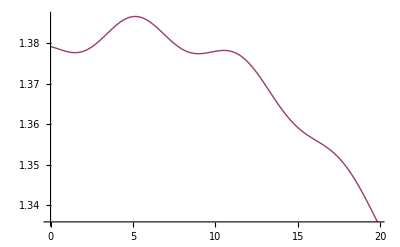

```mathematica
sx1data=ListPlot[{{times,2 avgspins[[All,4,3]]}ᵀ,{times,2avgspins[[All,1,3]]}ᵀ},Joined->True,PlotRange->All]
```

Part::partw: Part 5 of {{-0.0543948, -0.137348, 0.689594, -0.123729, -0.123372, 0.029752, -0.138307, -0.459743}, {« 19 », « 6 », -« 19 »}, {0.127037, 0.252688, -0.0134738, -0.0812167, -« 21 », 0.054221, 0.026733, 0.667574}} does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {{0, 5/32, 5/16, 15/32, 5/8, 25/32, 15/16, 35/32, 5/4, 45/32, 25/16, 55/32, 15/8, 65/32, 35/16, 75/32, 5/2, 85/32, 45/16, 95/32, 25/8, 105/32, 55/16, 115/32, 15/4, 125/32, 65/16, 135/32, 35/8, 145/32, 75/16, 155/32, 5, 165/32, 85/16, 175/32, 45/8, 185/32, 95/16, 195/32, 25/4, 205/32, 105/16, 215/32, 55/8, 225/32, 115/16, 235/32, 15/2, 245/32, « 78 »}, 2\ {« 1 »} ⟦ All, 5, 3 ⟧} cannot be transposed.

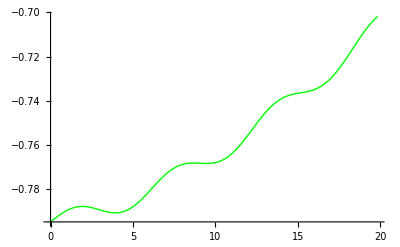

```mathematica
sx1data=ListPlot[{{times,2avgspins[[All,2,3]]}ᵀ,{times,2avgspins[[All,5,3]]}ᵀ},Joined->True,PlotRange->All, PlotStyle->Green]
```

Part::partw: Part 6 of {{-0.0543948, -0.137348, 0.689594, -0.123729, -0.123372, 0.029752, -0.138307, -0.459743}, {« 19 », « 6 », -« 19 »}, {0.127037, 0.252688, -0.0134738, -0.0812167, -« 21 », 0.054221, 0.026733, 0.667574}} does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {{0, 5/32, 5/16, 15/32, 5/8, 25/32, 15/16, 35/32, 5/4, 45/32, 25/16, 55/32, 15/8, 65/32, 35/16, 75/32, 5/2, 85/32, 45/16, 95/32, 25/8, 105/32, 55/16, 115/32, 15/4, 125/32, 65/16, 135/32, 35/8, 145/32, 75/16, 155/32, 5, 165/32, 85/16, 175/32, 45/8, 185/32, 95/16, 195/32, 25/4, 205/32, 105/16, 215/32, 55/8, 225/32, 115/16, 235/32, 15/2, 245/32, « 78 »}, 2\ {« 1 »} ⟦ All, 6, 3 ⟧} cannot be transposed.

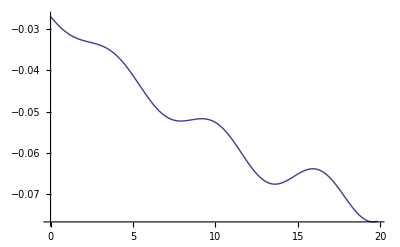

```mathematica
sx1data=ListPlot[{{times,2avgspins[[All,3,3]]}ᵀ,{times,2avgspins[[All,6,3]]}ᵀ},Joined->True,PlotRange->All]
```